```mathematica
ClearAll["Global`*"]
Needs["Notation`"]
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
```

```mathematica
Qi=-163/4;
Qf=-1033/32;
alpha=α;
gamma=Subscript[Q, 4] α;
lambda=Subscript[Q, λ] α;
```

```mathematica
Reduce[Qi<Subscript[Q, 4]<Qf&&alpha>0&&((gamma≤(4583 alpha)/208-3/208 √4079833 √(alpha^2)&&lambda≥7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2))||((4583 alpha)/208-3/208 √4079833 √(alpha^2)<gamma<(2013 alpha)/98-18/49 √5658 √(alpha^2)&&(1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)<lambda≤7/8 (77 alpha-2 gamma)-1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)||lambda≥7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)))||((2013 alpha)/98-18/49 √5658 √(alpha^2)≤gamma≤(157 alpha)/8&&lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2))||((157 alpha)/8<gamma≤(2013 alpha)/98+18/49 √5658 √(alpha^2)&&(-38 alpha≤lambda<1/2 (167 alpha+4 gamma)-√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)||lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)))||((2013 alpha)/98+18/49 √5658 √(alpha^2)<gamma<50 alpha&&(-38 alpha≤lambda≤7/8 (77 alpha-2 gamma)-1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)||7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)≤lambda<1/2 (167 alpha+4 gamma)-√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)||lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)))||(gamma==50 alpha&&(lambda==-38 alpha||7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)≤lambda<1/2 (167 alpha+4 gamma)-√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)||lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)))||(50 alpha<gamma<(4583 alpha)/208+3/208 √4079833 √(alpha^2)&&(7/8 (77 alpha-2 gamma)-1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)≤lambda≤-38 alpha||7/8 (77 alpha-2 gamma)+1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)≤lambda<1/2 (167 alpha+4 gamma)-√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)||lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2)))||((4583 alpha)/208+3/208 √4079833 √(alpha^2)≤gamma<100 alpha&&(7/8 (77 alpha-2 gamma)-1/8 √(-66951 alpha^2-8052 alpha gamma+196 gamma^2)≤lambda≤-38 alpha||lambda>1/2 (167 alpha+4 gamma)+√2 √(4300 alpha^2+557 alpha gamma-6 gamma^2))))]//N
```

-40.75<Q_4<-32.2813&&Q_λ≥-0.875 (-77.+2. Q_4)+0.125 √(-66951.-8052. Q_4+196. Q_4^2)&&α>0.

```mathematica
RegionPlot3D[Subscript[Q, λ]≥-0.875 (-77.+2. Subscript[Q, 4])+0.125 √(-66951.-8052. Subscript[Q, 4]+196. Subscript[Q, 4]^2),{Subscript[Q, 4],Qi,Qf},{Subscript[Q, λ],-200,2000},{α,10^-2,100},PlotStyle->Directive[Opacity[0.5]],Mesh->None]
```

-Graphics3D-

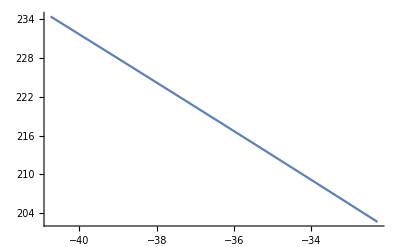

```mathematica
Plot[-0.875 (-77.+2. Subscript[Q, 4])+0.125 √(-66951.-8052. Subscript[Q, 4]+196. Subscript[Q, 4]^2),{Subscript[Q, 4],Qi,Qf}]
```